```mathematica
Needs["xxl`Main`"]
```

```mathematica
(167000-142500)/60//N
```

408.333

```mathematica
ListLinePlot[{{100,"1.050"},{200,"2.687"},{400,"8.683"},{800,"19.732"},{1600,"29.105"},{3200,"80.800"},{6400,"157.402"}},PlotLabel->"sleep",AxesLabel->{"n","ms/op"}]
```

-Graphics-

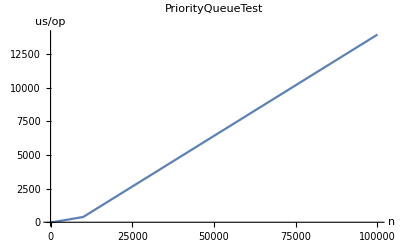

```mathematica
jmhPlot["Benchmark                        Mode  Cnt      Score       Error  Units
PriorityQueueTest.measure100     avgt    3      1.048 ±     0.133  us/op
PriorityQueueTest.measure1000    avgt    3     17.170 ±    15.631  us/op
PriorityQueueTest.measure10000   avgt    3    392.275 ±  1665.371  us/op
PriorityQueueTest.measure100000  avgt    3  13932.355 ± 41423.785  us/op"]
```